# Lab #6

## Craig Fox

Clear initial definitions

```mathematica
Remove["Global`*"]
```

3 Spring, 2 Block System

Initial Equations

```mathematica
eq1=x1''[t]+2w0^2*x1[t]-w0^2*x2[t]==0;
eq2=x2''[t]+2w0^2*x2[t]-w0^2*x1[t]==0;
sol = DSolve[{eq1,eq2,x1[0]==1,x1'[0]==0,x2[0]==0,x2'[0]==0},{x1,x2},t]
```

{{x1→Function[{t},1/4 ⅇ^(-ⅈ t w0-ⅈ √3 t w0) (ⅇ^(ⅈ t w0)+ⅇ^(ⅈ √3 t w0)+ⅇ^(2 ⅈ t w0+ⅈ √3 t w0)+ⅇ^(ⅈ t w0+2 ⅈ √3 t w0))],x2→Function[{t},-1/4 ⅇ^(-ⅈ t w0-ⅈ √3 t w0) (ⅇ^(ⅈ t w0)-ⅇ^(ⅈ √3 t w0)-ⅇ^(2 ⅈ t w0+ⅈ √3 t w0)+ⅇ^(ⅈ t w0+2 ⅈ √3 t w0))]}}

Position Graphs

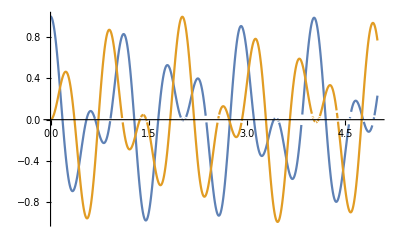

```mathematica
x1Solv = x1[t]/.sol[[1]]/.t->(T*2π*w0);
x2Solv = x2[t]/.sol[[1]]/.t->(T*2π*w0);
w0=1;
Plot[{x1Solv,x2Solv },{T,0,5 }]
```

Finding the Linear Combination Periods

```mathematica
Simplify[ComplexExpand[x1Solv+x2Solv]]
Simplify[ComplexExpand[x1Solv-x2Solv]]
```

Cos[2 π T]

Cos[2 √3 π T]

Linear Combination Graphs

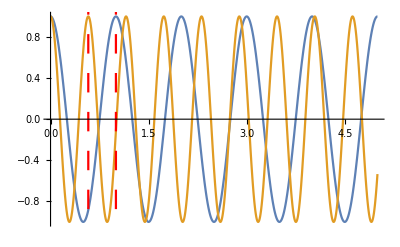

```mathematica
Show[Plot[{x1Solv+x2Solv,x1Solv-x2Solv},{T,0,5 }],ListLinePlot[{{1,-2},{1,2}},PlotStyle->{{Red,Dashing[Large]}}],ListLinePlot[{{1/(3^.5),-2},{1/(3^.5),2}},PlotStyle->{{Red,Dashing[Large]}}]]
```

3 Spring, 2 Block System

```mathematica
eq1=-3x1''[t]-w0^2*x1[t]+w0^2*(x2[t]-x1[t])==0;
eq2=-2x2''[t]-w0^2*(x2[t]-x1[t])==0;
sol = DSolve[{eq1,eq2,x1[0]==1,x1'[0]==0,x2[0]==0,x2'[0]==0},{x1,x2},t]
```

{{x1→Function[{t},1/5 (3 Cos[t]+2 Cos[t/(√6)])],x2→Function[{t},-3/5 (Cos[t]-Cos[t/(√6)])]}}

Position Graphs

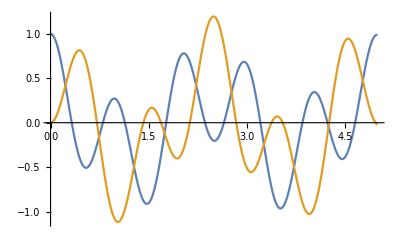

```mathematica
x1Solv = x1[t]/.sol[[1]]/.t->(T*2π*w0);
x2Solv = x2[t]/.sol[[1]]/.t->(T*2π*w0);
w0=1;
Plot[{x1Solv,x2Solv },{T,0,5 }]
```

Finding Linear Combination Periods

```mathematica
Simplify[ComplexExpand[x1Solv+x2Solv]]
Simplify[ComplexExpand[(3/2)*x1Solv-x2Solv]]
```

Cos[√(2/3) π T]

3/2 Cos[2 π T]

Linear Combination Graphs

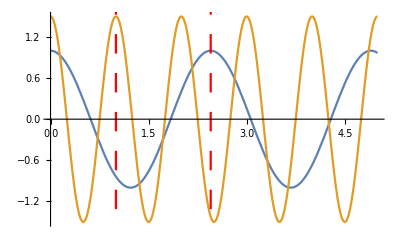

```mathematica
Show[Plot[{x1Solv+x2Solv,(3/2)*x1Solv-x2Solv},{T,0,5 }],ListLinePlot[{{6^.5,-2},{6^.5,2}},PlotStyle->{{Red,Dashing[Large]}}],ListLinePlot[{{1,-2},{1,2}},PlotStyle->{{Red,Dashing[Large]}}]]
```